```mathematica
city=StringJoin["dial"];
```

## Functions

### EdgeODBetweenessCentrality

```mathematica
EdgeODBetweenessCentrality::usage="EdgeODBetweenessCentrality[OD,G] gives a list of all origini-destination betweenness centralities for the edges in the graph G.";
EdgeODBetweenessCentrality[i_,j_,f_,G_]:=Module[
{b,k,q,P,eid,V,E,numberOfSkippedODPairs,ignoredVolume},
numberOfSkippedODPairs=0;
ignoredVolume=0;
V=VertexList[G];
E=EdgeList[G];
b=Association[Table[PropertyValue[{G,E[[k]]},EdgeLabels]->0,{k,Length[E]}]];
Monitor[
For[k=1,k<=Length[i],k++,
If[And[MemberQ[V,i[[k]]],MemberQ[V,j[[k]]]],
P=FindShortestPath[G,i[[k]],j[[k]]];
For[q=1,q<Length[P],q++,
eid=PropertyValue[{G,P[[q]]->P[[q+1]]},EdgeLabels];
b[eid]+=f[[k]]
],
numberOfSkippedODPairs++;
ignoredVolume+=f[[k]]
];
],
ProgressIndicator[k,{50,Length[i]}]
];
Print["numberOfSkippedODPairs = ",numberOfSkippedODPairs];
Print["ignoredVolume = ",ignoredVolume," (",ignoredVolume/Total[f]," of total volume)"];
Return[b];
];
```

## Load Data and Read Graph

### Read edges

#### Read edges data

```mathematica
fid=StringJoin["C:\\Users\\Michael\\gitrepos\\github\\network\\instances\\",city,"_edges_algbformat.txt"];
data=Import[fid,"Table","FieldSeparator"->" "];
Take[data,5]//TableForm
```

eid | source | target | dir | capacity | speed_mph | cost_time
20984 | 1 | 7361 | 1 | 950 | 20 | 0.579894
3780 | 1 | 27 | 1 | 950 | 20 | 0.044809
9968 | 2 | 2249 | 1 | 8100 | 40 | 0.439616
7447 | 3 | 9732 | 1 | 5400 | 40 | 0.0824052

#### Unpacking sources, targets and weights of edges

```mathematica
{eid=data[[2;;,1]],source=data[[2;;,2]],target=data[[2;;,3]],weights=data[[2;;,7]]};
```

#### Read node data

```mathematica
fid=StringJoin["C:\\Users\\Michael\\gitrepos\\github\\network\\instances\\",city,"_nodes_algbformat.txt"];
data=Import[fid,"Table","FieldSeparator"->" "]; Take[data,5]//TableForm
```

nid | lon | lat
1 | -8.54199 | 41.1299
2 | -8.59126 | 41.1965
3 | -8.62958 | 41.1794
4 | -8.63015 | 41.0924

#### Set nodes

```mathematica
{nid=data[[2;;,1]],lat=data[[2;;,3]],lon=data[[2;;,2]]};
nodes=Table[GeoPosition[{lat[[i]],lon[[i]]}],{i,Length[nid]}];
```

### Graph construction

```mathematica
edges=Table[source[[i]]->target[[i]],{i,Length[eid]}];
labels=Table[edges[[i]]->eid[[i]],{i,Length[eid]}];
coords=Table[{lon[[i]],lat[[i]]},{i,Length[nid]}];
G=Graph[nid,edges,EdgeWeight->weights,EdgeLabels->labels,VertexCoordinates->coords];
EdgesOfG=EdgeList[G];
VertexOfG=VertexList[G];
```

### Plot Graph

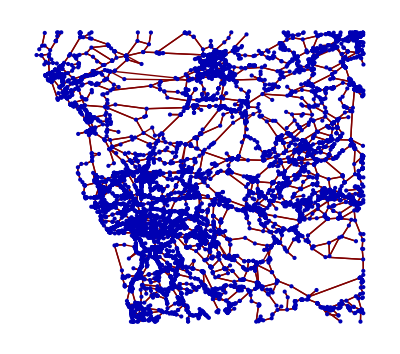

```mathematica
GraphPlot[G,VertexLabeling->False,DirectedEdges->False]
```

### Read MatOD

```mathematica
fid=StringJoin["C:\\Users\\Michael\\gitrepos\\github\\network\\instances\\",city,"_interod_0_1.txt"];
data=Import[fid,"Table","FieldSeparator"->" "]; Take[data,5]//TableForm
```

```mathematica
orig=data[[2;;,1]]
dest=data[[2;;,2]]
flow=data[[2;;,3]]
```

{3187,8782,197,768,20052,38488,39790,3961,3961,29,2353,38665,3429,3429,3265,10502,10502,2160,29072,22567,18965,13720,38091,25630,8338,230,38089,31005,30853,18927,34897,30715,25686,35923,36051,38252,28184,21192,10658,2263,3173,22264,16967,22504,25054,34100,18992,4987,511,38507,19962,19962,29938,35756,36525,27857,4687,24349,30619,2342114,22352,35112,6909,31756,34703,14412,34715,21975,13849,7406,30864,36699,28525,13429,29256,12557,12533,13497,22126,13510,8047,39129,13424,27684,8580,31530,19487,6152,33326,17680,37367,32624,8146,32625,38398,6864,6864,13071,6860,39475,21653,6864,17865,29324,4876,14059,3459,14059,35125,3002,5480,22156,7075,9345,39115,11149,10934,14495,14805}
 |  |  |  |

{29164,22612,4597,12620,33048,17943,40124,17692,14919,8069,13171,11202,21856,15007,11042,26135,33857,8505,33640,10841,1803,21322,37784,37786,21322,26050,34512,39812,11332,9941,31702,31734,9943,9941,9875,32062,9866,19440,15219,16643,13572,32656,37818,26082,2344,37816,3173,22273,22261,22264,26595,24825,40124,29693,11385,9662,26397,3147,2342116,1453,32490,10096,17380,6925,17625,19237,9947,23999,21676,25728,7192,26137,39782,7273,23461,10259,19686,3039,38607,7344,25015,26678,12633,34644,26567,14334,14334,31200,7603,34208,31957,23503,16809,33284,39760,2907,33284,33284,28278,34185,6186,12499,35847,22106,22834,10938,6478,14573,679,1074,20654,16885,14522,29270,23716,9935,9952}
 |  |  |  |

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,2.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,2.,1.,1.,1.,1.,1.,1.,1.,2342065,1.,1.,1.,1.,2.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,2.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,2.,1.,1.,1.,1.,1.,1.,2.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,7.,5.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}
 |  |  |  |

```mathematica
(* identifying matod pairs that are not in the city graph G *)
```

```mathematica
matodInvalidVertexSet=Complement[Union[orig,dest],VertexOfG];
```

```mathematica
matodValidVertexMap=Table[True,{i,Max[{Max[orig],Max[dest],Max[VertexOfG]}]}];
For[i=1,i≤Length[matodInvalidVertexSet],i++,
matodValidVertexMap[[matodInvalidVertexSet[[i]]]]=False
];
```

```mathematica
matodValidEdgeMap=Table[And[matodValidVertexMap[[orig[[i]]]],matodValidVertexMap[[dest[[i]]]]],{i,Length[orig]}]
Print["Ratio of removed edges:",Total[Table[If[matodValidEdgeMap[[i]],1,0],{i,Length[matodValidEdgeMap]}]]/Length[orig]]
```

{True,True,True,True,True,True,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,False,True,True,True,True,True,True,True,True,True,True,True,True,True,2342100,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,False,True,True,True,True,True,True,True,True,True,False,True,True,True,True,True,True,True,True,True,True,True,True}
 |  |  |  |

Ratio of removed edges:546749/585558

```mathematica
(* identifying matod pairs that are not connected *)
nonreachableEdgeSet={};
For[i=1,i≤Length[orig],i++,
If[Not[matodValidEdgeMap[[i]]],Continue[]];
If[GraphDistance[G,orig[[i]], dest[[i]]]===∞,
Print[{orig[[i]],dest[[i]]}];
AppendTo[nonreachableEdgeSet,{orig[[i]],dest[[i]]}];
]
]
```

```mathematica
(* save nonreachable pairs *)
Export[StringJoin["C:\\Users\\Michael\\gitrepos\\github\\network\\mathematica\\",city,"_nonreachable_pairs.csv"],nonreachableEdgeSet]
```

C:\Users\Michael\gitrepos\github\network\mathematica\sfbay_nonreachable_pairs.csv

## Set Ranks

#### Volume Over Capacity

```mathematica
(*fid=StringJoin["C:\\Users\\Michael\\Dropbox\\work.network\\code\\matlab\\instances\\mit_data\\instances\\",city,"_selfishflows_0_10.txt"];
data=Import[fid,"Table","FieldSeparator"->" "];
Take[data,5]//TableForm*)
```

#### EdgeBetweennessCentrality

```mathematica
Timing[btwc=EdgeBetweennessCentrality[G];]
```

{171.891,Null}

```mathematica
(* export EdgeBetweennessCentrality *)
table=Table[{eid[[i]],EdgesOfG[[i]][[1]],EdgesOfG[[i]][[2]],btwc[[i]]},{i,Length[eid]}];
fid=StringJoin["C:\\Users\\Michael\\gitrepos\\github\\network\\mathematica\\rank_",city,"_edge_betweenness_centrality.csv"];
Export[fid,table,TableHeadings->{"eid","source","target","EdgeBetweennessCentrality"}];
```

#### EdgeODBetweenessCentrality

```mathematica
(* Calculate EdgeODBetweenessCentrality *)
fid=StringJoin["C:\\Users\\Michael\\Dropbox\\work.network\\code\\matlab\\instances\\mit_data\\instances\\",city,"_interod_0_1.txt"];
data=Import[fid,"Table","FieldSeparator"->" "];
Timing[btod=EdgeODBetweenessCentrality[data[[2;;All,1]],data[[2;;All,2]],data[[2;;All,3]],G];]
```

numberOfSkippedODPairs = 54673

$Aborted

```mathematica
(* Export EdgeODBetweennessCentrality *)
table=Table[{eid[[i]],EdgesOfG[[i]][[1]],EdgesOfG[[i]][[2]],btod[[i]]},{i,Length[eid]}];
fid=StringJoin["C:\\Users\\Michael\\Dropbox\\work.network\\code\\matlab\\instances\\mit_data\\figures\\rank_",city,"_edge_od_betweenness_centrality.csv"];
Export[fid,table,TableHeadings->{"eid","source","target","EdgeODBetweennessCentrality"}];
```